```mathematica
NA = 6.0221367 10^23;
Dtot= 2 10^-12;
kd=10^3;
sigma=5 10^-9;
kf=10 * sigma * Dtot;
kD=4*Pi*sigma*Dtot;
h=(1+kf/kD)*Sqrt[Dtot]/sigma;
a=kd*Sqrt[Dtot]/sigma;
r0=sigma;
tau = sigma^2 / Dtot;
t= tau 10^-2;
maxr = 4.5 Sqrt[ 6 Dtot t]+sigma;
```

```mathematica
sol=N[Solve[{x+y+z==h, x*y+y*z+x*z==kd,x*y*z==a},{x,y,z}]];
alpha=sol[[1,1,2]];
beta = sol[[1,2,2]];
gamma=sol[[1,3,2]];
```

```mathematica
W[x_,y_]:=Exp[2*x*y+y^2]*Erfc[x+y];
frac[x_,y_,z_]:=(x*(z+x)*(x+y))/((z-x)*(x-y));
coeff[r_]:=1/(4*Pi*r*r0*Sqrt[Dtot]);
term1[r_]:=1/Sqrt[4*Pi*t]*(Exp[-(r-r0)^2/(4*Dtot*t)]+Exp[-(r+r0-2*sigma)^2/(4*Dtot*t)]);
term2[r_]:=frac[alpha,beta,gamma]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),alpha*Sqrt[t]];
term3[r_]:=frac[beta,gamma,alpha]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),beta*Sqrt[t]];
term4[r_]:=frac[gamma,alpha,beta]*W[(r+r0-2*sigma)/(Sqrt[4*Dtot*t]),gamma*Sqrt[t]];
```

```mathematica
f[r_]:=4*Pi*r^2*Re[coeff[r]*(term1[r]+term2[r]+term3[r]+term4[r])]
```

c = N[Integrate[f[r], {r, 1, Infinity}]]

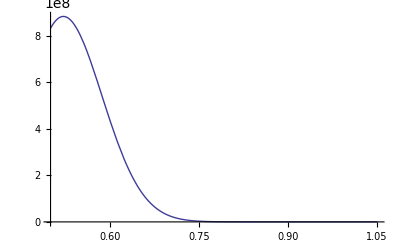

```mathematica
Plot[f[r], {r,sigma,maxr}]
```

```mathematica
out:=Table[{r,f[r]},{r,sigma,maxr,(maxr - sigma) / 1000}] // N
```

```mathematica
Export["p_rev.-2.tsv",out]
```

p_rev.-2.tsv